## Calculating the Value of Machine Epsilon with loops

### Using While Loop

```mathematica
(* when e becomes less than machine epsilon, Mathematica will ignore it in computations *)
Clear["Global`*"]

e = 1;
While[1.0 + e /2- 1.0 != 0, 
If[1.0 + e /2- 1.0 == 0 , Break];
e = e/2
]
(* The value of e is Machine epsilon now *)
N[e]
```

2.22045×10^-16

### Using For Loop

```mathematica
e = 1;
For[e=1,1.0 + e/2 -1.0 != 0, e = e/2 , Continue]
N[e]
```

2.22045×10^-16

## The Gaussian Function

```mathematica
u[x_,σ_ , μ_:0] := x^(2) Exp[-((x-μ)/σ)^2  /2] /(σ Sqrt[2 Pi])
u[x,σ]
```

(ⅇ^(-x^2/(2 σ^2)) x^2)/(√(2 π) σ)

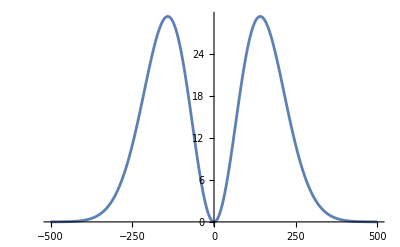

```mathematica
(* Test for σ = 100 *)
TestData = Table[{x,u[x,100 , 0]} , {x , -500,500,1}];
ListLinePlot[TestData]
```

### Creating the various values of σ

```mathematica
list1 = {1/1000};

(* Making 55 sample points that are evenly spaced in a decade *)
Do[AppendTo[list1 , list1[[-1]] + 10^(Floor[Log[10,list1[[-1]]]])] , 54] 
N[list1]
```

{0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,200.,300.,400.,500.,600.,700.,800.,900.,1000.}

```mathematica
(*  Making 120 Logarithmic Linear sample points *)
list2 = {};
upperLimit = 1000;
lowerLimit = 1/1000;
numberOfSteps = 120;
stepSize = (Log[10,upperLimit] - Log[10,lowerLimit])/(numberOfSteps - 1);
AppendTo[list2,lowerLimit];
Do[AppendTo[list2 , 10^(Log[10,list2[[-1]]] + stepSize)], numberOfSteps -1];
(* N[list2] *)
```

### Integrating For the values of σ from List1 and List2 and Plotting them

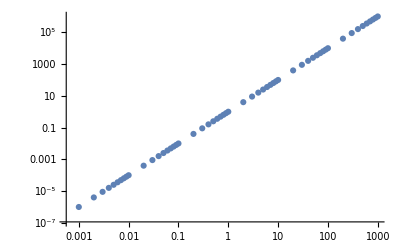

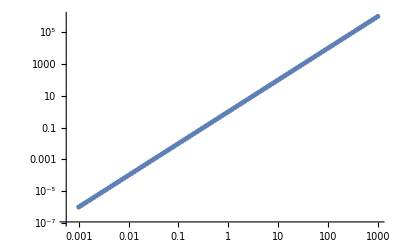

```mathematica
(* Integrating for Values of σ from list1 and making custom range for each element *)
I1 = {# , NIntegrate[u[x,#] , {x,-#*10,#*10}]}&/@list1;
plt1 = ListLogLogPlot[I1, PlotRange->All]
I2 = {# , NIntegrate[u[x,#] , {x,-#*10,#*10}]}&/@list2;
plt2 = ListLogLogPlot[I2, PlotRange->All]
```